# TEST 1: τ(t)

A and B simultaneously diagonalizable

```mathematica
P={{1,0,0},{-2,1,0},{-1,1,1}};
A0={{-200,0,0},{0,-30,0},{0,0,-10}};
B=P.{{-158,0,0},{0,-20.,0},{0,0,-9.99}}.Inverse[P];
A=P.A0.Inverse[P];
s[t_]:=1-E^(-t);
g[t_]:=3/4+1/2*Cos[t];
ysol[t_]:={Cos[t/25],Sin[t/10]^2-E^(-t/50),2+t/100};
f[t_]:=ysol'[t]-A.ysol[t]-s[t]*B.ysol[t-g[t]]
f[t]
```

{200 Cos[t/25]-(1-ⅇ^-t) (0.-158. Cos[1/25 (-3/4+t-Cos[t]/2)])-1/25 Sin[t/25],ⅇ^(-t/50)/50-340 Cos[t/25]+1/5 Cos[t/10] Sin[t/10]+30 (-ⅇ^(-t/50)+Sin[t/10]^2)-(1-ⅇ^-t) (0.+276. Cos[1/25 (-3/4+t-Cos[t]/2)]-20. (-ⅇ^(1/50 (3/4-t+Cos[t]/2))+Sin[1/10 (-3/4+t-Cos[t]/2)]^2)),1/100+10 (2+t/100)-150 Cos[t/25]+20 (-ⅇ^(-t/50)+Sin[t/10]^2)-(1-ⅇ^-t) (-9.99 (2+1/100 (-3/4+t-Cos[t]/2))+127.99 Cos[1/25 (-3/4+t-Cos[t]/2)]-10.01 (-ⅇ^(1/50 (3/4-t+Cos[t]/2))+Sin[1/10 (-3/4+t-Cos[t]/2)]^2))}

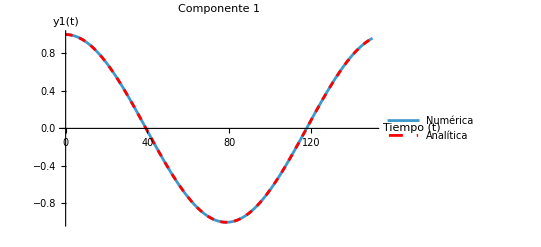

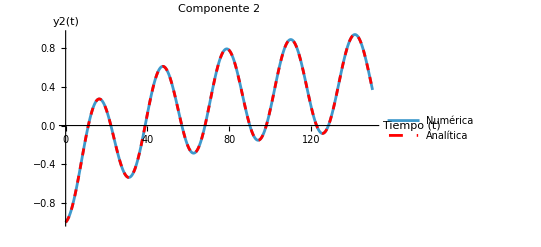

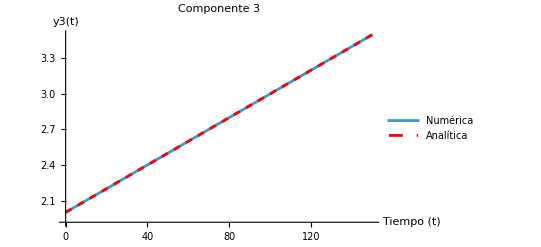

Última iteración: 150.05

Errores en la última iteración: 	 Componente 1 = 8.85447×10^-11, 	 Componente 2 = 1.05769×10^-7, 	 Componente 3 = 1.58084×10^-7

```mathematica
(*Coeficientes del método*)
a0=0;
a1=-1 ;
a2=1 ;
b0=1/2 ;
b1=-1/2 ;
b2=1;
b0s=1/2;
b1s=-1/2;
b2s=1;

(*Tamaño del paso*)
h=0.05; (*IMPORTANTE: debe ser estrictamente menor que el mínimo de g(t)=0.25, para que cuando interpolemos la interpolación no use nodos aun no determinados*)


(*Tiempo inicial y final*)
tInicial=0;
tFinal=150;
numPasos=Round[(tFinal-tInicial)/h];

(*Condición inicial y el historial inicial*)
yInicial=ysol[tInicial];
yHistoryList={ysol[tInicial]};

yEvalList[t_]:=Module[{index},index=Round[(t-tInicial)/h];
If[index<0||index+1>Length[yHistoryList],Print["Error: Valor de y en tiempo ",t," (índice ",index,") no encontrado en el historial (lista)."];
Abort[],
yHistoryList[[index+1]]]];

(*Función auxiliar para evaluar y(t_retardado) usando interpolación cuadrática (3 nodos)*)evalDelayed[tEval_]:=Module[{k,θ,tDif,yNodeMinus1,yNode0,yNodePlus1,safeY},tDif=tEval-g[tEval];
If[tDif<tInicial,ysol[tDif],(*Usa historia analítica previa a tInicial*)(*k es el índice del nodo base inmediatamente por debajo de tDif*)k=Floor[(tDif-tInicial)/h];
θ=(tDif-(tInicial+k*h))/h;(*Parámetro normalizado entre 0 y 1*)
(*Función para devolver valores:Si el índice de un nodo pide un tiempo en el pasado (t<tInicial), usa ysol, sino se usa el historial calculado.*)
selectY[idx_]:=Module[{tNode=tInicial+idx*h},If[tNode<tInicial,ysol[tNode],yEvalList[tNode]]];
(*Obtenemos los valores en los 3 nodos (k-1,k,k+1)*)
yNodeMinus1=selectY[k-1];
yNode0=selectY[k];
yNodePlus1=selectY[k+1];
(*Interpolación Cuadrática usando los polinomios de Lagrange*)
(θ*(θ-1)/2)*yNodeMinus1+(1-θ^2)*yNode0+(θ*(θ+1)/2)*yNodePlus1]];

(*Definimos la función a emplear en cada iteración para calcular la solución numérica con el método*)
stepList[time_]:=Module[{n=Round[(time-tInicial)/h],ynPlus1Approx,sol,matrixM,vectorDerecha,errVector,ErrorComponent1,ErrorComponent2,ErrorComponent3,errAbs},
(*Se verifica que se esté haciendo la iteración correcta*)
If[n<0||n+1>Length[yHistoryList],
Print["Condición inicial fallida, n<0 o faltan entradas en el historial para continuar, en tiempo: ",time+2*h];Return[{}]]; 

(*Para el caso n=0 necesitamos obtener una aproximación (método de Euler) para y_1, para poder usarlo en el método*)
If[n+2>Length[yHistoryList]&&n+1<=numPasos, 
ynPlus1Approx=yEvalList[time]+h*(A.yEvalList[time]+f[time]+s[time]*B.ysol[time-g[time]]);
AppendTo[yHistoryList,ynPlus1Approx];AppendTo[solutionList,{time+h,ynPlus1Approx,{Abs[ysol[time+h][[1]]-ynPlus1Approx[[1]]],Abs[ysol[time+h][[2]]-ynPlus1Approx[[2]]],Abs[ysol[time+h][[3]]-ynPlus1Approx[[3]]]}}]];

(*Se comprueba que en el último paso se esté haciendo la iteración correctamente*)
If[Length[yHistoryList]<n+2,Print["Longitud del historial insuficiente en tiempo: ",time+2*h];Return[{}]];

matrixM=a2*IdentityMatrix[3]-h*b2*A;

vectorDerecha=-a1*yEvalList[time+h]-a0*yEvalList[time]+h*b1*(A.yEvalList[time+h]+f[time+h])+h*b0*(A.yEvalList[time]+f[time])+h*(b2s*s[time+2*h]*B.evalDelayed[time+2*h]+b1s*s[time+h]*B.evalDelayed[time+h]+b0s*s[time]*B.evalDelayed[time])+h*b2*f[time+2*h];

(*Calculamos y_{n+2} tal que M.y_{n+2}=vectorDerecha*)
sol=LinearSolve[matrixM,vectorDerecha];
If[sol=!={}&&FreeQ[sol,Indeterminate|ComplexInfinity],AppendTo[yHistoryList,sol];
errVector=ysol[time+2*h]-sol;
ErrorComponent1=Abs[errVector[[1]]];
	ErrorComponent2=Abs[errVector[[2]]];
	ErrorComponent3=Abs[errVector[[3]]];
errAbs={ErrorComponent1,ErrorComponent2,ErrorComponent3};
Return[{time+2*h,sol,errAbs}],Print["No se pudo resolver para y en el paso ",time+2*h,". sol = ",sol];
Return[{}]];];




(*Inicializamos la lista solución: {paso,vector solución, vector error}*)
solutionList={{tInicial,yHistoryList[[1]],{0,0,0}}};
currentTimeList=tInicial;


(*Este es el bucle que recorre el tiempo desde tInicial hasta tFinal, si la solución en un determinado paso es vacía (por algún error) no se inserta en la lista solución*)
While[currentTimeList<tFinal,
nextStepResultList=stepList[currentTimeList];
If[nextStepResultList!={},AppendTo[solutionList,Take[nextStepResultList,3]];(*Añade a la lista los 3 elementos obtenidos de stepList*)
currentTimeList+=h,Break[]];];


(*Graficamos la solución numérica y la analítica, componente a componente*)
numericalTimes=solutionList[[All,1]];
numericalSolComponents=Transpose[solutionList[[All,2]]];
ySolComponent1[t_]:=ysol[t][[1]]
ySolComponent2[t_]:=ysol[t][[2]]
ySolComponent3[t_]:=ysol[t][[3]]
plotComponent1=Plot[{ySolComponent1[t]},{t,tInicial,tFinal},PlotStyle->{Red,Dashed},PlotLegends->{"Analítica"}];
plotNumerical1=ListPlot[Transpose[{numericalTimes,numericalSolComponents[[1]]}],PlotStyle->Solid,PlotLegends->{"Numérica"},Joined->True];
Show[plotNumerical1,plotComponent1,PlotLabel->"Componente 1",AxesLabel->{"Tiempo (t)","y1(t)"}]

plotComponent2=Plot[{ySolComponent2[t]},{t,tInicial,tFinal},PlotStyle->{Red,Dashed},PlotLegends->{"Analítica"}];
plotNumerical2=ListPlot[Transpose[{numericalTimes,numericalSolComponents[[2]]}],PlotStyle->Solid,PlotLegends->{"Numérica"},Joined->True];
Show[plotNumerical2,plotComponent2,PlotLabel->"Componente 2",AxesLabel->{"Tiempo (t)","y2(t)"}]

plotComponent3=Plot[{ySolComponent3[t]},{t,tInicial,tFinal},PlotStyle->{Red,Dashed},PlotLegends->{"Analítica"}];
plotNumerical3=ListPlot[Transpose[{numericalTimes,numericalSolComponents[[3]]}],PlotStyle->Solid,PlotLegends->{"Numérica"},Joined->True];
Show[plotNumerical3,plotComponent3,PlotLabel->"Componente 3",AxesLabel->{"Tiempo (t)","y3(t)"}]


(*Imprimimos los valores de los errores en cada componente en la última iteración*)
lastEntry=Last[solutionList];
lastTime=lastEntry[[1]];
lastErrors=lastEntry[[3]];

Print["Última iteración: ",lastTime];
Print["Errores en la última iteración: \t Componente 1 = ",lastErrors[[1]],", \t Componente 2 = ",lastErrors[[2]],", \t Componente 3 = ",lastErrors[[3]]];
```

```mathematica
Log[4,(Sqrt[(2.338*10^-10)^2+(2.754*10^-7)^2+(4.153*10^-7)^2])/(Sqrt[(4.958*10^-12)^2+(1.736*10^-8)^2+(2.725*10^-8)^2])]
```

1.97351